## Peebles-Vilenkin 模型的quintessence 演化

```mathematica
UnitConvert[Quantity[, "UniverseCriticalMassDensity"] Quantity[, "SpeedOfLight"]^5 Quantity[, "ReducedPlanckConstant"]^3,^4]
```

4.×10^-47 GeV^4

```mathematica
V[ϕ_]:=(λ M^8)/(ϕ^4+M^4);
V'[ϕ[t]]
```

-(4 M^8 λ ϕ[t]^3)/((M^4+ϕ[t]^4)^2)

```mathematica
m=4.2*10^18;(*Planck mass*)
λ=1*10^-14;
M=8*10^5;
rh=0.3*3.7*10^-47;
```

```mathematica
Reduce[V[ϕ]==0.7*3.7*10^-47&&ϕ>0,ϕ]
```

ϕ==8.97129×10^19

```mathematica
T=2*10^44;
sol=NDSolve[{3 a'[t]/a[t] ϕ'[t]==(4 M^8 λ ϕ[t]^3)/((M^4+ϕ[t]^4)^2),a'[t]/a[t]==1/m √(V[ϕ[t]]+rh a[t]^-3),a[0]==1,ϕ[0]==8.971292837140387*^19},{a[t],ϕ[t]},{t,0,T},MaxSteps->10000]
```

{{a[t]→InterpolatingFunction[…][t],ϕ[t]→InterpolatingFunction[…][t]}}

```mathematica
Plot[Evaluate[a[t]/.sol[[1]]],{t,0,T},AxesLabel->{"t","a[t]"}]
Plot[Evaluate[ϕ[t]/.sol[[1]]],{t,0,T},AxesLabel->{"t","ϕ[t]"}]
```

-Graphics-

-Graphics-

### Frozen and attractor quintessence

最终加速膨胀态

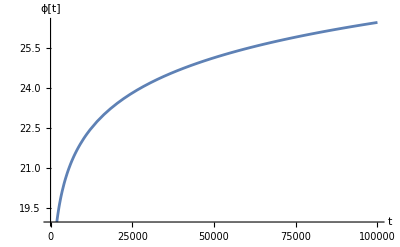

```mathematica
Clear["Global`*"]  
m=10;
T=100000;
PHI0=10;
V[ϕ_]:=Exp[-(ϕ-PHI0)](ϕ/PHI0)^-1;
eqn=ϕ''[t]+3 √((8 Pi)/3(1/2 m ϕ'[t]^2+V[ϕ[t]]))ϕ'[t]+V'[ϕ[t]]==0;

sol=NDSolve[{eqn,ϕ'[0]==0.00,ϕ[0]==PHI0},ϕ[t],{t,0,T}];
Plot[Evaluate[ϕ[t]/.sol],{t,0,T},AxesLabel->{"t","ϕ[t]"}]
```

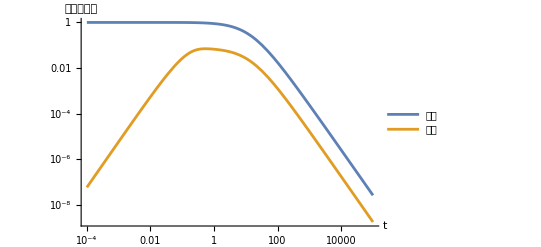

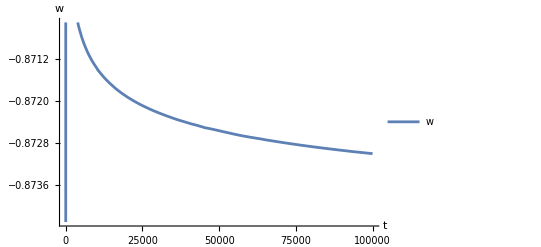

```mathematica
Po=V[ϕ[t]/. sol];
Ki=1/2 m (D[ϕ[t]/. sol,t])^2;
LogLogPlot[Evaluate[{Po,Ki}],{t,0.0001,T},AxesLabel->{"t","动能，势能"},PlotLegends->Placed[{"势能","动能"}, {Top,Right}]]
Plot[Evaluate[(Ki-Po)/(Ki+Po)],{t,0,T},AxesLabel->{"t","w"},PlotLegends->Placed[{"w"}, {Top,Right}]]
```

调整动能项权重，最终达到减速膨胀态

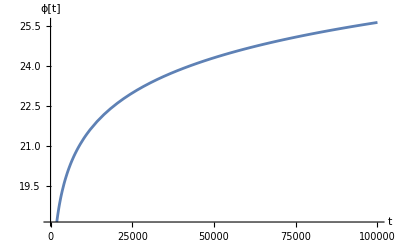

```mathematica
Clear["Global`*"]  
m=500;
T=100000;
PHI0=10;
V[ϕ_]:=Exp[-(ϕ-PHI0)](ϕ/PHI0)^-1;
eqn=ϕ''[t]+3 √((8 Pi)/3(1/2 m ϕ'[t]^2+V[ϕ[t]]))ϕ'[t]+V'[ϕ[t]]==0;

sol=NDSolve[{eqn,ϕ'[0]==0.00,ϕ[0]==PHI0},ϕ[t],{t,0,T}];
Plot[Evaluate[ϕ[t]/.sol],{t,0,T},AxesLabel->{"t","ϕ[t]"}]
```

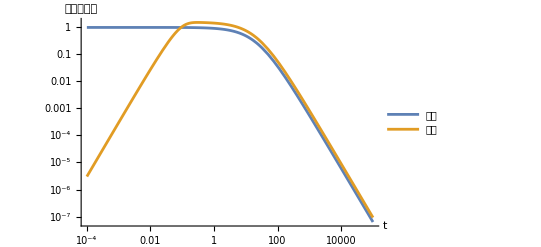

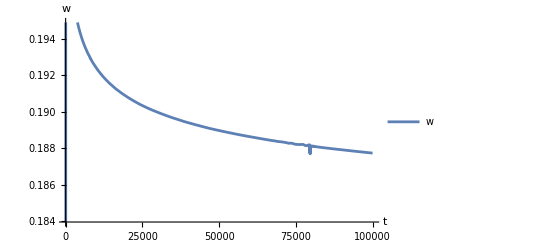

```mathematica
Po=V[ϕ[t]/. sol];
Ki=1/2 m (D[ϕ[t]/. sol,t])^2;
LogLogPlot[Evaluate[{Po,Ki}],{t,0.0001,T},AxesLabel->{"t","动能，势能"},PlotLegends->Placed[{"势能","动能"}, {Top,Right}]]
Plot[Evaluate[(Ki-Po)/(Ki+Po)],{t,0,T},AxesLabel->{"t","w"},PlotLegends->Placed[{"w"}, {Top,Right}]]
```

## 背景物质主导下标量场动能、势能演化

```mathematica
λ=1;
M=1;
V[ϕ_]:=(λ M^8)/(ϕ^4+M^4);
```

```mathematica
Reduce[V[ϕ]==1/2&&ϕ>0,ϕ]
```

ϕ==1

```mathematica
Tb=4000;
H=2/(3(1+w)t)/.w->0;

eq=ϕ''[t]+3H ϕ'[t]+V'[ϕ[t]]==0;
ic={ϕ'[0.001]==10,ϕ[0.001]==2};
solb=NDSolve[{eq,ic},ϕ[t],{t,0.001,Tb}]
```

{{ϕ[t]→InterpolatingFunction[…][t]}}

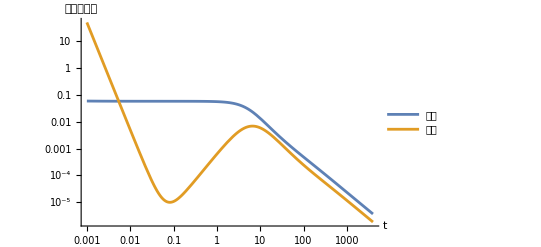

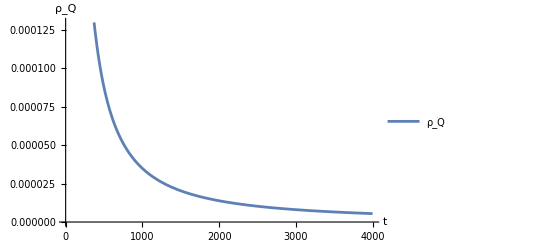

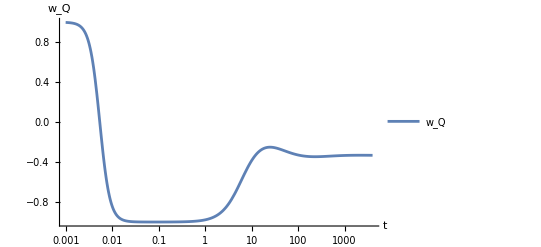

```mathematica
Po=V[ϕ[t]/. solb];
Ki=1/2 (D[ϕ[t]/. solb,t])^2;
LogLogPlot[Evaluate[{Po,Ki}],{t,0.001,Tb},AxesLabel->{"t","动能，势能"},PlotLegends->Placed[{"势能","动能"}, {Top,Right}],PlotRange->All]

Plot[Evaluate[Ki+Po],{t,0.001,Tb},AxesLabel->{"t","ρ_Q"},PlotLegends->Placed[{"ρ_Q"}, {Top,Right}]]

LogLinearPlot[Evaluate[(Ki-Po)/(Ki+Po)],{t,0.001,Tb},AxesLabel->{"t","w_Q"},PlotLegends->Placed[{"w_Q"}, {Top,Right}]]
```

### 单一标量场演化

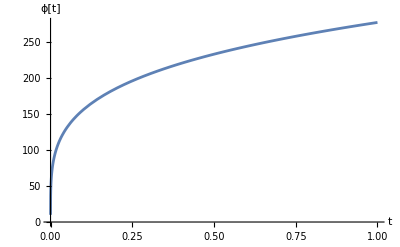

```mathematica
Clear["Global`*"]  
λ=0.1;
M=1;
V[ϕ_]:=(λ M^8)/(ϕ^4+M^4);
T=10^10;
eqn=ϕ''[t]+3 √(8(1/2 ϕ'[t]^2+V[ϕ[t]]))ϕ'[t]+V'[ϕ[t]]==0;

sol=NDSolve[{eqn,ϕ'[0]==0.0000,ϕ[0]==10},ϕ[t],{t,0,T}];
Plot[Evaluate[ϕ[t]/.sol],{t,0,T},AxesLabel->{"t","ϕ[t]"}]
```

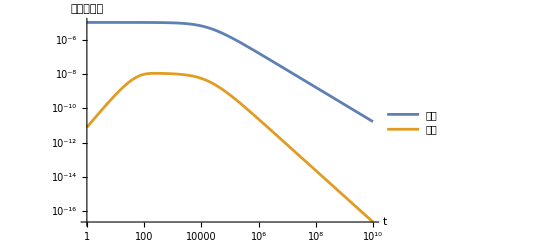

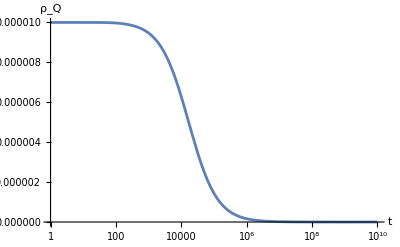

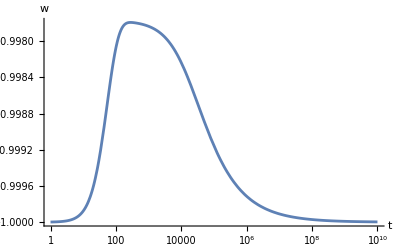

```mathematica
Po=V[ϕ[t]/. sol];
Ki=1/2 (D[ϕ[t]/. sol,t])^2;
LogLogPlot[Evaluate[{Po,Ki}],{t,1,T},AxesLabel->{"t","动能，势能"},PlotLegends->Placed[{"势能","动能"}, {Top,Right}]]
LogLinearPlot[Evaluate[Ki+Po],{t,1,T},AxesLabel->{"t","ρ_Q"}]
LogLinearPlot[Evaluate[(Ki-Po)/(Ki+Po)],{t,1,T},AxesLabel->{"t","w"},PlotRange->All]
```

换个势能形式

```mathematica
Clear["Global`*"]  

T=10^20;
PHI0=10;

V[ϕ_]:=10^3 Exp[-(ϕ-PHI0)^1.5](ϕ/PHI0)^-3;
eqn=ϕ''[t]+3 √(8 (1/2 ϕ'[t]^2+V[ϕ[t]]))ϕ'[t]+V'[ϕ[t]]==0;

sol=NDSolve[{eqn,ϕ'[0]==0.00,ϕ[0]==PHI0},ϕ[t],{t,0,T}]
Po=V[ϕ[t]/. sol];
Ki=1/2(D[ϕ[t]/. sol,t])^2;
LogLogPlot[Evaluate[{Po,Ki}],{t,0.01,T},AxesLabel->{"t","动能，势能"},PlotLegends->Placed[{"势能","动能"}, {Top,Right}]]
LogLinearPlot[Evaluate[(Ki-Po)/(Ki+Po)],{t,0.01,T},AxesLabel->{"t","w"},PlotRange->All]
```

{{ϕ[t]→InterpolatingFunction[…][t]}}

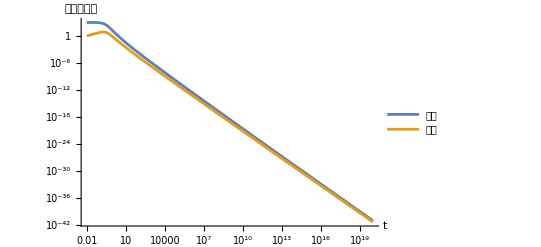

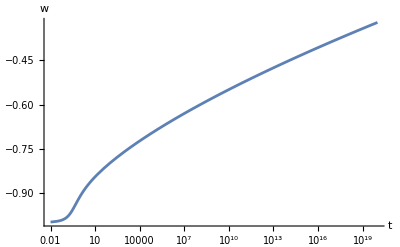

## The exponential quintessence tail

```mathematica
V[ϕ_]:=Exp[-ϕ];
H=2/(3(1+w)t)/.w->0;
```

```mathematica
T=10^6
eq=ϕ''[t]+3H ϕ'[t]+V'[ϕ[t]]==0;
ic={ϕ[0.001]==1,ϕ'[0.001]==0};
solb=NDSolve[{eq,ic},ϕ[t],{t,0.001,T}];
Po=V[ϕ[t]/. solb];
Ki=1/2 (D[ϕ[t]/. solb,t])^2;
```

1000000

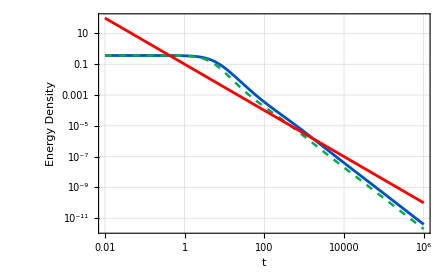

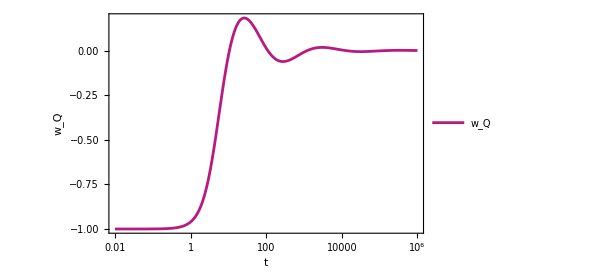

```mathematica
Show[
LogLogPlot[Evaluate[Po+Ki],{t,0.01,T},PlotLegends->Placed[{"ρ_ϕ"},{Right,Top}],PlotStyle->{RGBColor[0,0.32,0.77]},PlotRange->All],
LogLogPlot[Evaluate[Po],{t,0.01,T},PlotLegends->Placed[{"V[ϕ]"},{Right,Top}],PlotStyle->{Thickness[0.004],RGBColor[0,0.68,0.29],Dashed},PlotRange->All],
LogLogPlot[0.1 t^(-3/2),{t,0.01,T},PlotLegends->Placed[{"ρ_B"}, {Right,Top}],PlotStyle->{Red},PlotRange->All],
Frame->True,GridLines->Automatic,

FrameLabel->{"t","Energy Density"}
]

LogLinearPlot[Evaluate[(Ki-Po)/(Ki+Po)],{t,0.01,T},PlotStyle->{RGBColor[0.72,0.1,0.5]},FrameLabel->{"t","w_Q"},PlotLegends->Placed[{"w_Q"}, {Right,Bottom}],Frame->True,GridLines->Automatic]
```